```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/benjamin/Dokumente/Programme/stripey honeycomb

```mathematica
γ[x_,y_]:=1/3*Sqrt[1+4*Cos[x/2]^2+4*Cos[x/2]*Cos[Sqrt[3]/2*y]];
A[x_,y_]:=1;
B[x_,y_]:=γ[x,y];
ϵ[x_,y_]:=3*Sqrt[A[x,y]^2-B[x,y]^2];
```

```mathematica
n=32;
kx=1;
ky=0.5;
numeric=Import["eigenvalues.dat","Data"];
justenergies=Table[numeric[[i]][[2]],{i,1,Length[numeric]}];
analytic=Table[{ϵ[x*2π*kx/n,y*π/n],ϵ[x*2*π*ky/n,y*2*π/n]},{x,0,n-1},{y,0,n-1}];
```

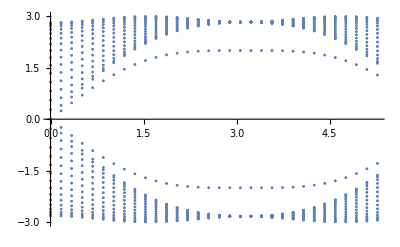

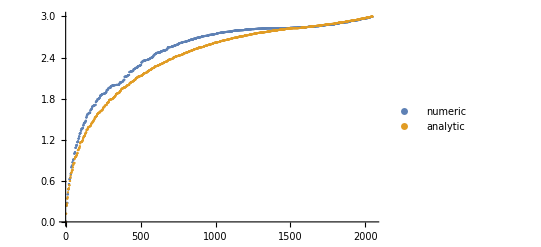

```mathematica
ListPlot[numeric]
ListPlot[{Sort[Flatten[Abs[justenergies]]],Sort[Flatten[N[analytic]]]},PlotLegends->{"numeric","analytic"}]
```